## 1. Solving TOV equations.

### 1.1 Equation of state:

#### 1.1.1 Relativistic Case (pure NS)

Let’s try first just this one: relativistic case

```mathematica
Pressure R[ϵ_]:=ϵ/3;
Density R[p_]:=3p;
```

#### 1.1.2 Non Relativistic Case (pure NS)

Pressure and density take the following form

```mathematica
ϵ(P) = 5 (m/(15 π^2 λ^3))^(2/5)P^(3/5)
```

with m, λ of the gas we are considering, let’s say neutrons only, then

```mathematica
m=1.67 10^-24;
c = 2.99792458 10^10;
lambda=2.1 10^-14;
k =5((m c^2)/(15 π^2 lambda^3))^(0.4);
(*   Functions:    *)
Density NR[p_]:=k p^0.6
Pressure NR[ϵ_]:= (ϵ/k)^5/3
```

#### 1.1.3 Whole Range Neutron Star (Pure NS)

We need first to define density and pressure as function of non-dimensional fermi momentum

```mathematica
n = m c^2/(Pi^2*lambda^3);
epsilon[z_]:=n/8 ((2z^3+z)Sqrt[1+z^2]-ArcSinh[z])
pres[z_]:=n/8((2z^3 /3-z)Sqrt[1+z^2]+ArcSinh[z])
```

now, we create a table of data (p, ϵ):

```mathematica
d1 = Table[{pressure[z],epsilon[z]},{z,10.^-3,10^-2,10^-5}];
d2 =Table[{pressure[z],epsilon[z]},{z,10.^-2,10^-1,10^-4}];
d3=Table[{pressure[z],epsilon[z]},{z,10.^-1,10^0,10^-3}];
d4=Table[{pressure[z],epsilon[z]},{z,10.^0,10^1,10^-2}];
d5=Table[{pressure[z],epsilon[z]},{z,10.^1,10^2,10^-1}];
d6=Table[{pressure[z],epsilon[z]},{z,10.^2,10^3,10^0}];
```

```mathematica
density n=Union[d1,d2,d3,d4,d5,d6];
Density NS = Interpolation[density n,InterpolationOrder->100];
```

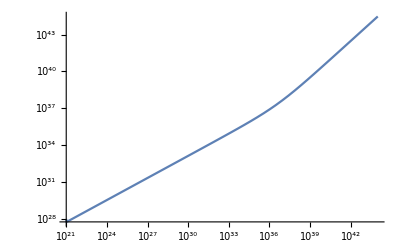

```mathematica
LogLogPlot[Density NS[x],{x,10^21,10^44}]
```

Now, let’s build the function for the whole range as a picewise function taking the R and NR approx,

```mathematica
pw=Piecewise[{{Density NR[x], 0≤  x<10^23}, {Density NS[x],10^23≤ x≤ 10^45},{Density R[x],x>10^45}}];
dener[p_]:=pw/.x-> p
```

#### Constants

We need to declare the following constants

```mathematica
G = 6.673 10^-8;
Subscript[M, sol]=1.9891 10^33;
c = 2.99792458 10^10;
α=G Subscript[M, sol]/(10^5 c^2);
Subscript[E0, sol]= Subscript[M, sol] c^2;
km3 = (10.0^5)^3;
rmin = 0.001;
rmax = 350;
densup = 7.86;
```

The numerical values of the constants to non-dimensionalise the equations are:

```mathematica
beta[Pc_]:=4 Pi Pc km3 /Subscript[E0, sol]
β =beta[10^35];
{α,β}
```

{1.47685,0.00070293}

Now we can proceed to do the numerical integration

#### Newton Equations:

We solve first this simple case.

```mathematica
Pc = 3.3 10^34;
ListRG={};
Do[
{solutionN = NDSolve[{p'[r]== If[p[r]>0,-(α dener[p[r]*Pc]*M[r])/(Pc r^2),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],p[rmin]==1,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass ad[x_]:=M[x]/.solutionN[[1]];
pressure ad[x_]:=p[x]/.solutionN[[1]];
If[pressure ad[rad]==0,
Break[],
ListRG=Append[ListRG,{rad,dener[Pc*pressure ad[rad]]}]
];
},
{rad,rmin+0.1,25,.1}]
```

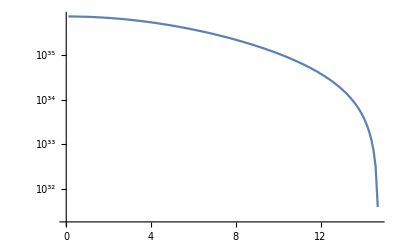

```mathematica
ListLogPlot[ListRG,Joined->True]
```

#### TOV Equations:

```mathematica
Pc = 3.3 10^34;
Listϵ={};
Listp={};
Do[{ 
solutionTOV = NDSolve[
{p'[r]== If[p[r]>0,-α*(M[r]+(4 π (Pc km3)/Subscript[E0, sol])r^3 p[r] )(dener[p[r]*Pc]/Pc+p[r])/(r(r - 2 α  M[r])),0.0],
M'[r]==If[p[r]>0,(4 π (Pc km3)/Subscript[E0, sol]) r^2 dener[p[r] Pc]/Pc,0.0],
p[rmin]==1.0,M[rmin]==0.0},{p,M},{r,rmin,rad},MaxSteps->Infinity];
mass[x_]:=M[x]/.solutionTOV[[1]];
TOVpressure[x_]:=p[x]/.solutionTOV[[1]];
If[TOVpressure[rad]==0,
Break[],
Listϵ=Append[Listϵ,{rad,dener[Pc*TOVpressure[rad]]/Pc}];
Listp=Append[Listp,{rad,TOVpressure[rad]}];
R=rad
];
},{rad,rmin+0.1,15,.1}]
```

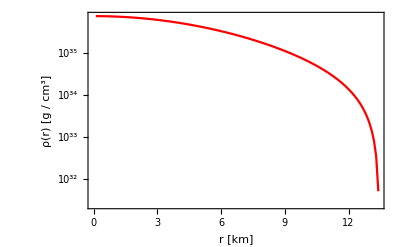

```mathematica
PureNSDensity=ListLogPlot[Listϵ,Joined->True,
Frame->True,
PlotStyle->Red,
FrameLabel->{"r [km]","ρ(r) [g / cm^3]"}]
```

```mathematica
Export["Plots/PureNS_Density.pdf",PureNSDensity];
```

### Gravity Tunnel inside the NS (Pure case)

#### Classical Case

Interpolation of the density

```mathematica
ρ N = Interpolation[ListTOV,InterpolationOrder->10]
```

InterpolatingFunction[…]

Velocity profile

```mathematica
v n [r_]:=Sqrt[8 Pi G NIntegrate[ρ n[x] x^2/y^2,{y,r,R},{x,0,y}]]
```

```mathematica
Plot[v n[r],{r,rmin,R}]
```

-Graphics-

```mathematica
T n = 2 NIntegrate[1/v n[r],{r,0,R}]
```

1.51921×10^-34

#### General Relativity Case

First, define non dimensional functions for energy density and pressure (they are both in terms of central pressure)

```mathematica
ϵ n = Interpolation[Listϵ,InterpolationOrder->10]
p n = Interpolation[Listp,InterpolationOrder->10]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

Along with the non-dimensional mass, this will be useful to define the metric tensor component functions:

```mathematica
Subscript[g, rr](r)=A(r) = (1 - (2 G M(r))/r)^-1 = (1 - 2α (M̄)/r)^-1
```

with M̄ in units of solar masses and r in km. Then

```mathematica
A[r_]:= (1 - 2 α TOVmass[r]/r)^-1
```

and the other function comes from the diff. eq.

```mathematica
(B'(r))/(B(r))= - (2 P'(r))/(P(r)+ϵ(r))
```

with boundary conditions in the surface equal to the Schwarzschild solution for the exterior metric:

```mathematica
1- (2 α)/R
```

0.779591

written next:

```mathematica
BFunction=NDSolve[ {Bb'[r] == -2 Bb[r] p n'[r]/(p n[r]+ϵ n[r]),Bb[R]== 0.78},Bb[r],{r,rmin+0.1,R}]
B[r_]=Bb[r]/.BFunction[[1]];
```

{{Bb[r]→InterpolatingFunction[…][r]}}

with  A=g_rr and B=g_tt, we already have all the components of the metric. The general energy diff. eq. is

```mathematica
1/2(dr/dτ)^2+1/2 g^rr(r)(1 - g^tt(r) E^2)=0
```